```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  1

fixed point ~ -20.1312

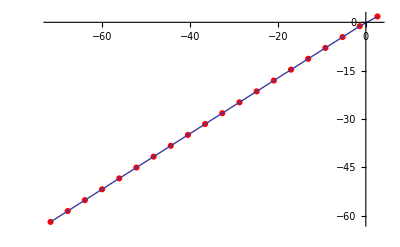

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  2

fixed point ~ -21.9855

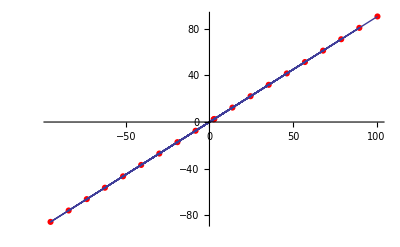

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  3

fixed point ~ -24.0011

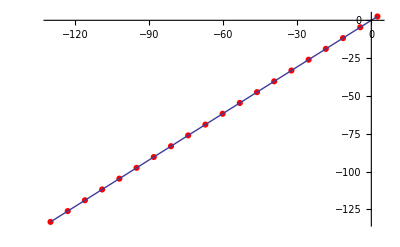

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  4

fixed point ~ -25.9999

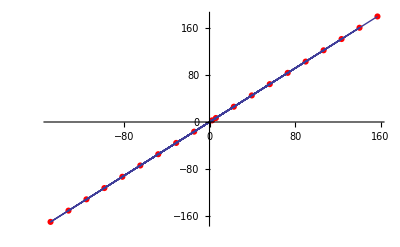

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  5

fixed point ~ -28.

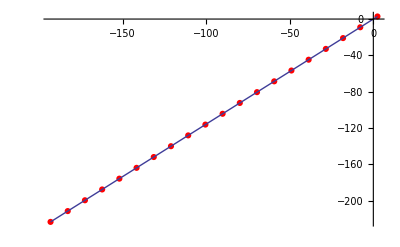

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  6

fixed point ~ -30.

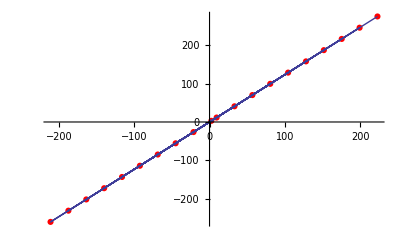

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  7

fixed point ~ -32.

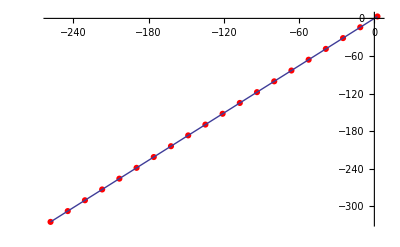

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  8

fixed point ~ -34.

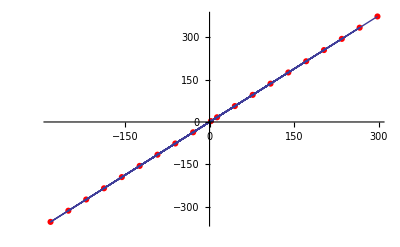

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  9

fixed point ~ -36.

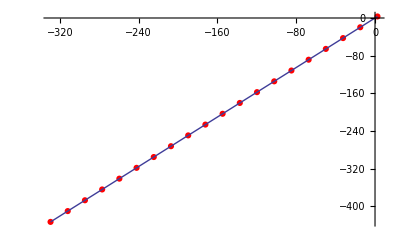

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  10

fixed point ~ -38.

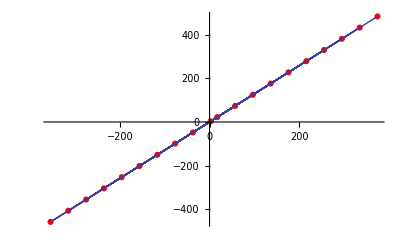

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  11

fixed point ~ -40.

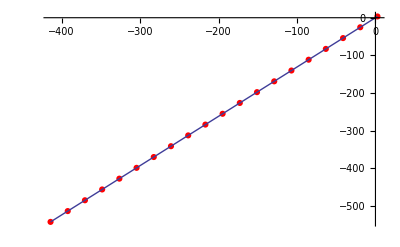

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  12

fixed point ~ -42.

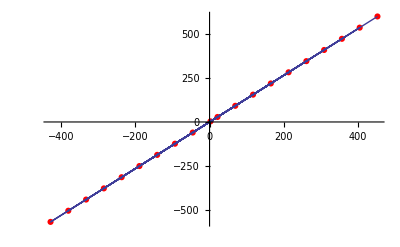

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  13

fixed point ~ -44.

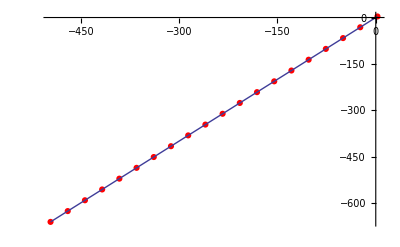

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  14

fixed point ~ -46.

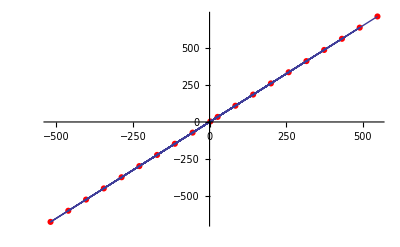

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  15

fixed point ~ -48.

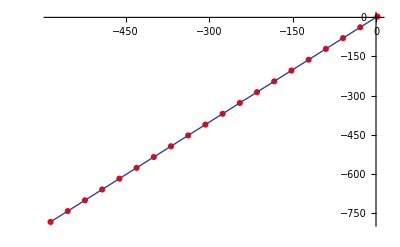

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  16

fixed point ~ -50.

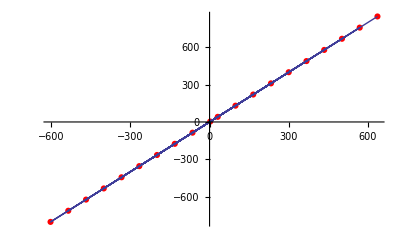

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  17

fixed point ~ -52.

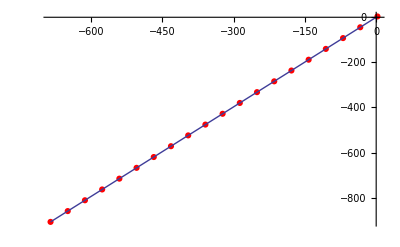

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  18

fixed point ~ -54.

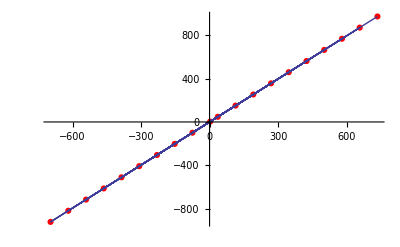

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  19

fixed point ~ -56.

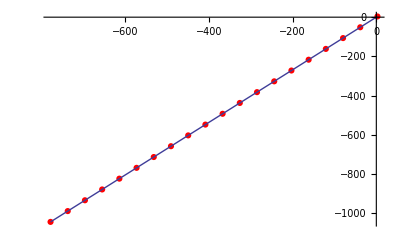

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  20

fixed point ~ -58.

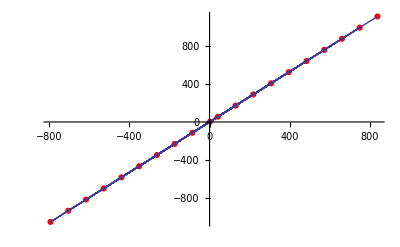

elasped seconds   6035.90731

```mathematica
start=SessionTime[];
streamzeros=OpenRead["barryzerosprecision1000no8"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxptsprecision1000no1"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenWrite["realfxNrhoNrun1jun16no11"];
precision=1000;
For[n=0,n<20,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*betterbarryzeroslist[[n,2]];
fx=fxlist[[n,2]];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<20,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]]
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  21

fixed point ~ -60.

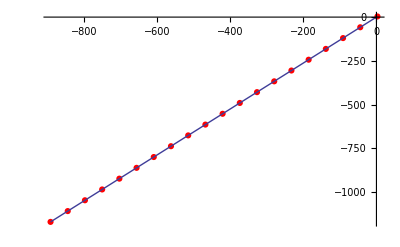

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  22

fixed point ~ -62.

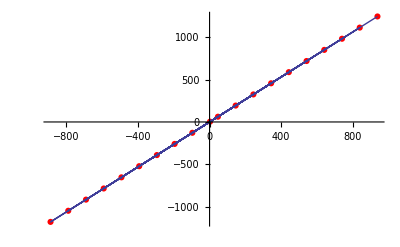

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  23

fixed point ~ -64.

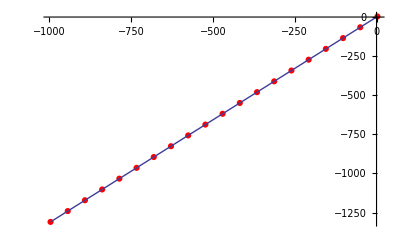

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  24

fixed point ~ -66.

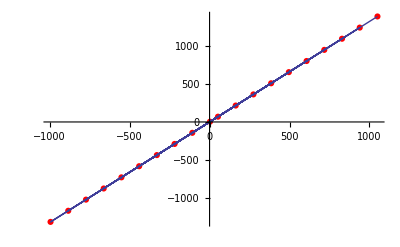

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  25

fixed point ~ -68.

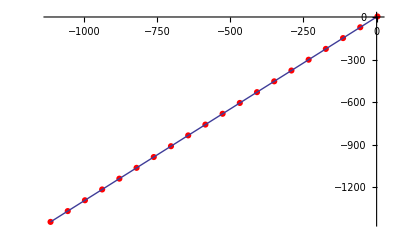

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  26

fixed point ~ -70.

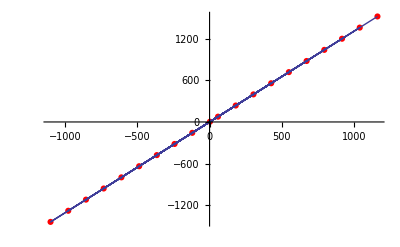

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  27

fixed point ~ -72.

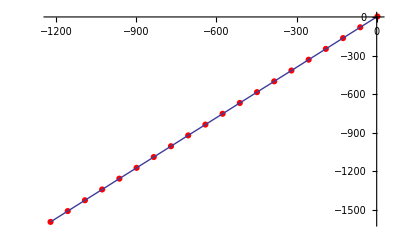

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  28

fixed point ~ -74.

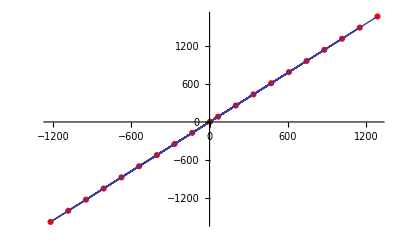

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  29

fixed point ~ -76.

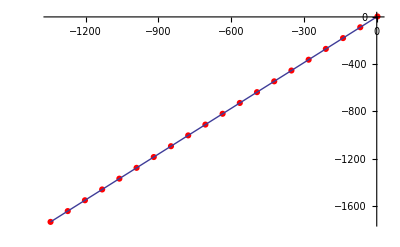

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  30

fixed point ~ -78.

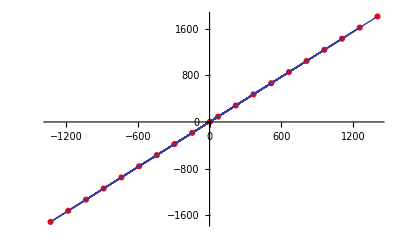

elasped seconds   1582.04311

```mathematica
start=SessionTime[];
streamzeros=OpenRead["barryzerosprecision1000no8"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxptsprecision1000no1"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenAppend["realfxNrhoNrun1jun16no11"];
precision=1000;
For[n=20,n<30,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*betterbarryzeroslist[[n,2]];
fx=fxlist[[n,2]];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<20,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]]
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  31

fixed point ~ -80.

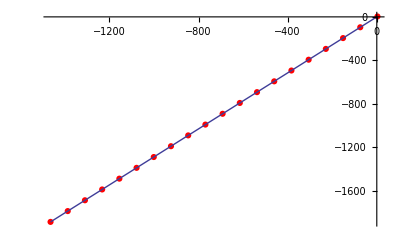

elasped seconds   134.42095

```mathematica
start=SessionTime[];
streamzeros=OpenRead["barryzerosprecision1000no8"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxptsprecision1000no1"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenAppend["realfxNrhoNrun1jun16no11"];
precision=1000;
For[n=30,n<31,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*betterbarryzeroslist[[n,2]];
fx=fxlist[[n,2]];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<20,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]]
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  32

fixed point ~ -82.

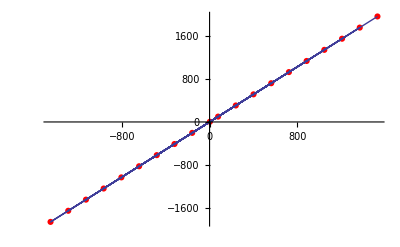

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  33

fixed point ~ -84.

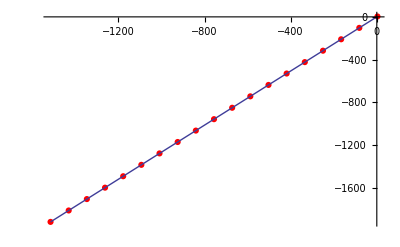

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  34

fixed point ~ -86.

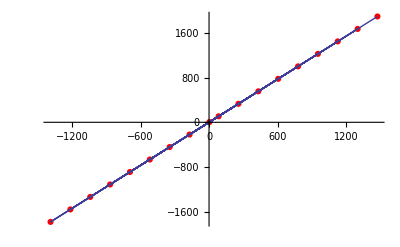

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  35

fixed point ~ -88.

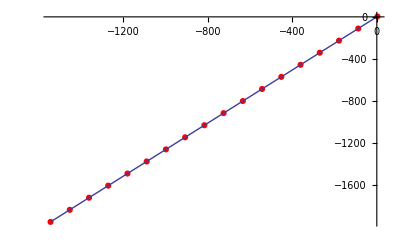

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  36

fixed point ~ -90.

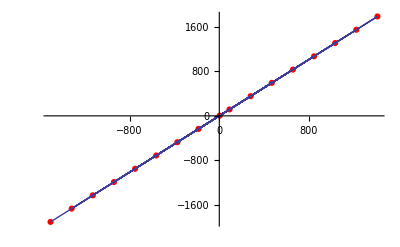

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  37

fixed point ~ -92.

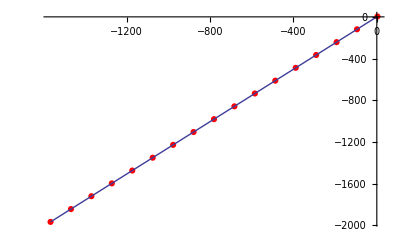

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  38

fixed point ~ -94.

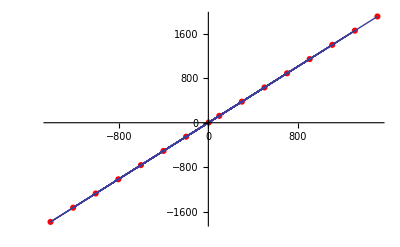

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  39

fixed point ~ -96.

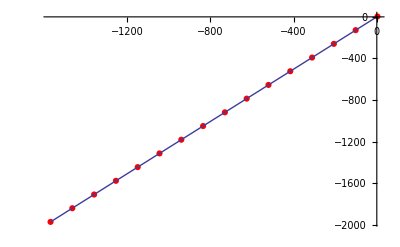

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  40

fixed point ~ -98.

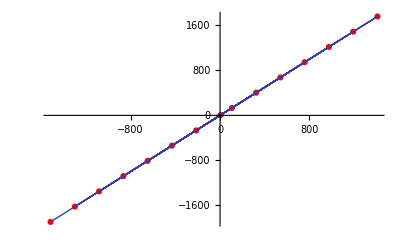

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  41

fixed point ~ -100.

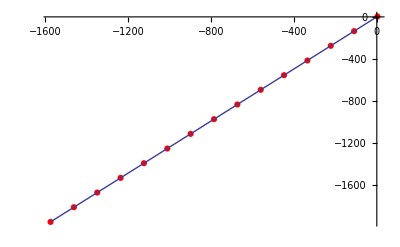

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  42

fixed point ~ -102.

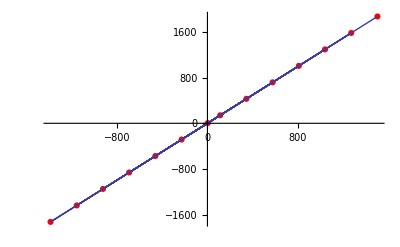

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  43

fixed point ~ -104.

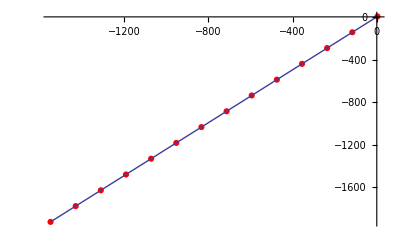

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  44

fixed point ~ -106.

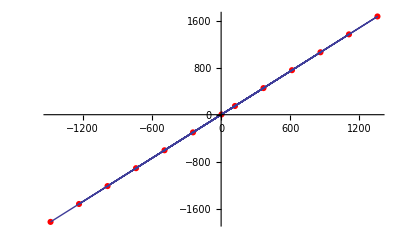

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  45

fixed point ~ -108.

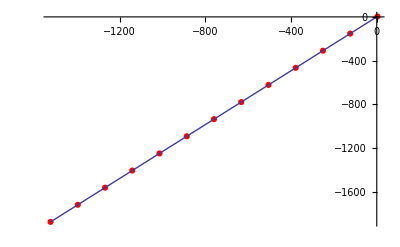

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  46

fixed point ~ -110.

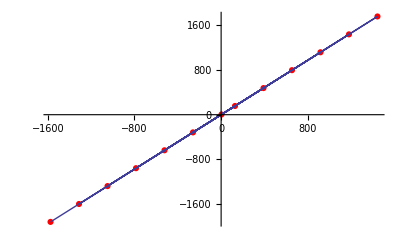

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  47

fixed point ~ -112.

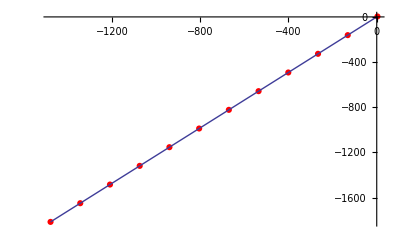

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  48

fixed point ~ -114.

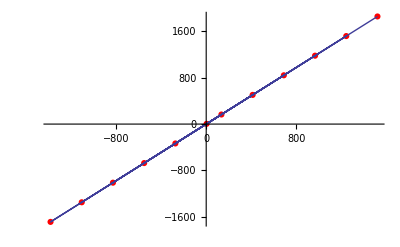

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  49

fixed point ~ -116.

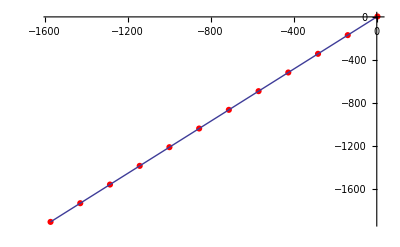

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  50

fixed point ~ -118.

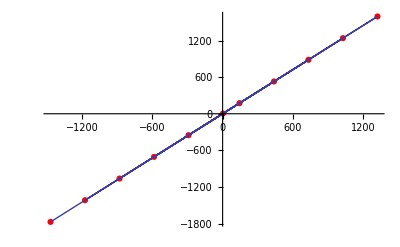

elasped seconds   1778.87784

```mathematica
start=SessionTime[];
streamzeros=OpenRead["barryzerosprecision1000no8"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxptsprecision1000no1"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenAppend["realfxNrhoNrun1jun16no11"];
precision=1000;
For[n=31,n<50,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*betterbarryzeroslist[[n,2]];
fx=fxlist[[n,2]];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<20,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]]
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```